```mathematica
Integrate[Exp[- k^2](Cosh[√(k^2+1)]),{k,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-k^2) Cosh[√(1+k^2)]ⅆk

```mathematica
NIntegrate[Exp[- k^2](Exp[√(k^2+1)]),{k,-∞,∞}]
```

6.09693

```mathematica
Integrate[Exp[- k^2](Cosh[k]),{k,∞,∞}]
```

0

```mathematica
NIntegrate[Exp[- k^2](Cosh[√((k+1)^2+1)]),{k,-∞,∞}]
```

4.74795

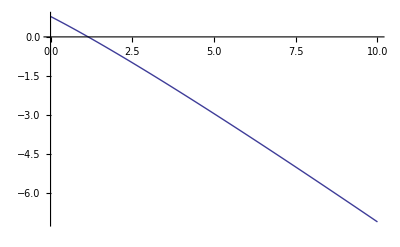

```mathematica
Plot[-y+Log[NIntegrate[Exp[-2 k^2](Cosh[√((k+1)^2+y)]),{k,-∞,∞}]],{y,0,10}]
```

```mathematica
Integrate[Exp[-b/2 k^2 ]2Cosh[b(kr k+d)],{k,-∞,∞}]
```

ConditionalExpression[(2 ⅇ^((b kr^2)/2) √(2 π) Cosh[b d])/(√b),Re[b]>0]